```mathematica
Load["MH0", "MH2"];
Ring3DCC=buildCC3D[{
	{{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}},
	{{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}},
	{{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}},
	{{1,1},{1,1},{1,1},{0,0},{0,0},{1,1},{1,1},{1,1}},
	{{1,1},{1,1},{1,1},{0,0},{0,0},{1,1},{1,1},{1,1}},
	{{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}},
	{{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}},
	{{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}}
}];
horse4=buildCC2D[threshold[Reverse[ImportGray["M2/horse_64.png"]],N[100/255]]];
tShape6=buildCC3D[Get["M2/tshape.dat"]];
```

Testing 1

Example 1

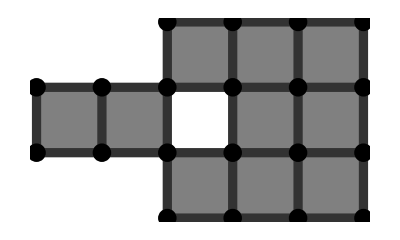

```mathematica
arrC={{0,0,1,1,1},{1,1,0,1,1},{0,0,1,1,1}};
showCC2D[buildCC2D[arrC]]
```

Example 2

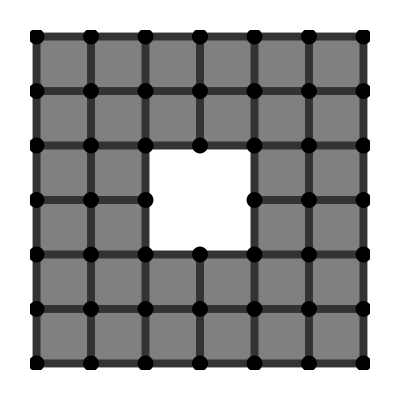

```mathematica
arrRing={{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,0,0,1,1},{1,1,0,0,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1}};
showCC2D[buildCC2D[arrRing]]
```

Example 3

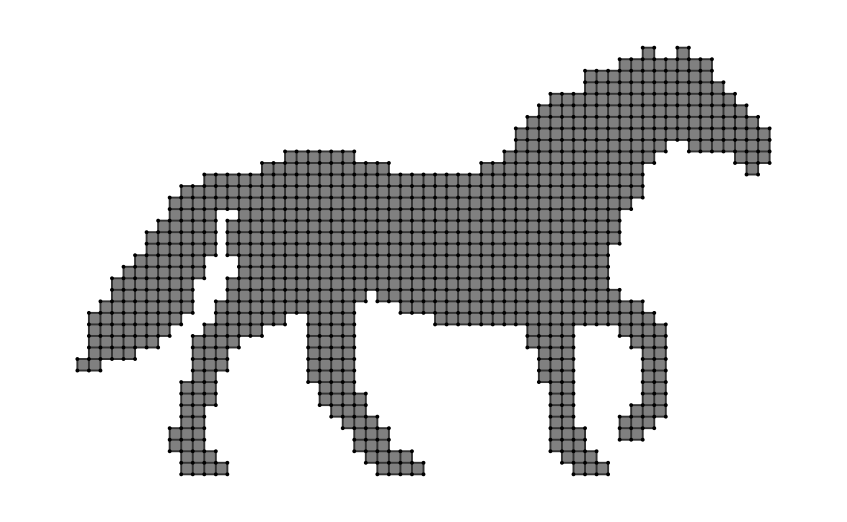

```mathematica
showCC2D[horse4]
```

Testing 2

Example 1

```mathematica
arrC3D={{{0,0},{0,0},{1,0},{1,0},{1,0}},{{1,0},{1,0},{0,0},{1,0},{1,0}},{{0,0},{0,0},{1,0},{1,0},{1,0}}};
showCC3DExt[buildCC3D[arrC3D]]
```

-Graphics3D-

```mathematica
showCC3DExt[Ring3DCC]
```

-Graphics3D-

```mathematica
showCC3DExt[tShape6]
```

-Graphics3D-

Testing 3

```mathematica
showCC3DExt[Nest[thinExhaustive,Ring3DCC,7]]
```

-Graphics3D-

Testing 4

Example 1

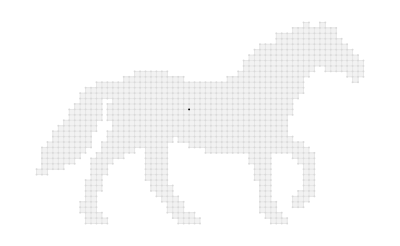

```mathematica
showCC2D[thin[horse4,{{Infinity,1}}],horse4]
```

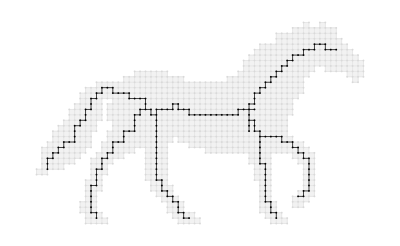

```mathematica
showCC2D[thin[horse4,{{4,.4}}],horse4]
```

```mathematica
showCC3D[thin[tShape6,{}],tShape6]
```

-Graphics3D-

```mathematica
showCC3D[thin[tShape6,{{∞,1},{7,.5}}],tShape6]
```

-Graphics3D-

```mathematica
showCC3D[thin[tShape6,{{4,.4},{∞,1}}],tShape6]
```

-Graphics3D-

```mathematica
showCC3D[thin[tShape6,{{4,.4},{5,.5}}],tShape6]
```

-Graphics3D-

Problem 1

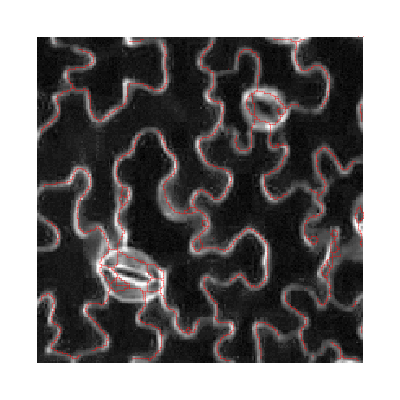

```mathematica
img1=Reverse[ImportGray["M2/epidermis.png"]];
cc1=buildCC2D[threshold[img1,0.09]];
showCC2DImg[thin[cc1,{{5,.5},{∞,1}}],img1]
```

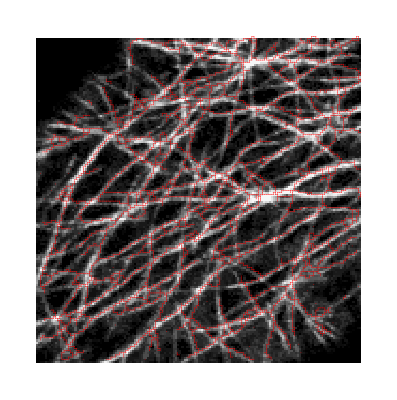

```mathematica
img2=Reverse[ImportGray["M2/filament_part.png"]];
cc2=buildCC2D[threshold[img2,0.238]];
showCC2DImg[thin[cc2,{{5,.5}}],img2]
```

```mathematica
img3=Get["M2/hand.dat"];
cc3=buildCC3D[img3];
```

```mathematica
showCC3D[thin[cc3,{{5,.5},{5,.5}}],cc3]
```

-Graphics3D-

```mathematica
showCC3D[thin[cc3,{{4,.4},{∞,1}}],cc3]
```

-Graphics3D-

```mathematica
showCC3D[thin[cc3,{{∞,1},{4,.4}}],cc3]
```

-Graphics3D-